# 3DOIT ζ_(4b)

```mathematica
e=1.60 10^-19;
m=6.65 10^-26;
Ω=6 10^9;
r0=3 10^-3;
V0=200;
U0=1 10^-6;

a=A[e,U0,m,r0,Ω];
q=Q[e,V0,m,r0,Ω];
β=5 10^-3;

NoP=6;
time=30000;

Q[e_,V0_,m_,r0_,Ω_]:=(2 e V0)/(m r0^4 Ω^2);
A[e_,U0_,m_,r0_,Ω_]:=(2 e U0)/(m r0^4 Ω^2);
coul[v_,i_,j_]:=D[e^2/((Subscript[x, i][τ]-Subscript[x, j][τ])^2+(Subscript[y, i][τ]-Subscript[y, j][τ])^2+(Subscript[z, i][τ]-Subscript[z, j][τ])^2),v];
c[v_,i_]:=- 1/(m Ω^2 π 8.85 10^-12)Sum[If[i≠j,coul[v,i,j],0],{j,1,NoP}];


EQS[α_,χ_]:=Table[{Subscript[x, i]''[τ]==(α+2 q Cos[2τ])(6 Subscript[x, i][τ]Subscript[y, i][τ]Subscript[z, i][τ])-β Subscript[x, i]'[τ]+χ c[Subscript[x, i][τ],i],
Subscript[y, i]''[τ]==(α+2 q Cos[2τ])(3(Subscript[x, i][τ])^2 Subscript[z, i][τ]-(Subscript[z, i][τ])^3)-β Subscript[y, i]'[τ]+χ c[Subscript[y, i][τ],i],
Subscript[z, i]''[τ]==(α+2 q Cos[2τ])(3(Subscript[x, i][τ])^2 Subscript[y, i][τ]-3 Subscript[y, i][τ](Subscript[z, i][τ])^2)-β Subscript[z, i]'[τ]+χ c[Subscript[z, i][τ],i]},{i,1,NoP}];

INI[α_]:={Subscript[x, 1]'[0]==0,Subscript[y, 1]'[0]==0,Subscript[z, 1]'[0]==0,
Subscript[x, 1][0]==-(√α)/(√2 3^0.25 q),Subscript[y, 1][0]==-(√2 √α)/(3 3^0.25 q),Subscript[z, 1][0]==-(√α)/(√2 3^0.75 q),
Subscript[x, 2]'[0]==0,Subscript[y, 2]'[0]==0,Subscript[z, 2]'[0]==0,
Subscript[x, 2][0]==(√α)/(√2 3^0.25 q),Subscript[y, 2][0]==-(√2 √α)/(3 3^0.25 q),Subscript[z, 2][0]==-(√α)/(√2 3^0.75 q),
Subscript[x, 3]'[0]==0,Subscript[y, 3]'[0]==0,Subscript[z, 3]'[0]==0,
Subscript[x, 3][0]==-(√α)/(√2 3^0.25 q),Subscript[y, 3][0]==(√2 √α)/(3 3^0.25 q),Subscript[z, 3][0]==(√α)/(√2 3^0.75 q),
Subscript[x, 4]'[0]==0,Subscript[y, 4]'[0]==0,Subscript[z, 4]'[0]==0,
Subscript[x, 4][0]==(√α)/(√2 3^0.25 q),Subscript[y, 4][0]==(√2 √α)/(3 3^0.25 q),Subscript[z, 4][0]==(√α)/(√2 3^0.75 q),
Subscript[x, 5]'[0]==0,Subscript[y, 5]'[0]==0,Subscript[z, 5]'[0]==0,
Subscript[x, 5][0]==0,Subscript[y, 5][0]==(√2 √α)/(3 3^0.25 q),Subscript[z, 5][0]==-(2 √α)/(√2 3^0.75 q),
Subscript[x, 6]'[0]==0,Subscript[y, 6]'[0]==0,Subscript[z, 6]'[0]==0,
Subscript[x, 6][0]==0,Subscript[y, 6][0]==-(√2 √α)/(3 3^0.25 q),Subscript[z, 6][0]==(2 √α)/(√2 3^0.75 q)};

VAR=Flatten[Table[{Subscript[x, i],Subscript[y, i],Subscript[z, i]},{i,1,NoP}]];

NDS[α_,χ_]:=NDSolveValue[{EQS[α,χ],INI[α]},VAR,{τ,0,time}];
(*NDS[α_,χ_]:=NDSolveValue[{EQS[α,χ],INI[α]},VAR,{τ,0,time}];*)
```

```mathematica
(*NDS[α_,χ_]:=NDSolve[{EQS[α,χ],INI[α]},VAR,{τ,0,time}];
ParametricPlot3D[Evaluate[Table[({Subscript[x, i][τ],Subscript[y, i][τ],Subscript[z, i][τ]}/.NDS[0.000004,1]),{i,1,NoP}]],{τ,0,time}, PlotRange->{{-.5,.5},{-.5,.5},{-.5,.5}}]*)
```

## time-stab

```mathematica
renew0=Table[{(k a m r0^4 Ω^2)/(2 e),1/(√3)((NDS[k a,1][[1]][time]/((-√(k a))/(√2 3^0.25 q)))^2+(NDS[k a,1][[2]][time]/((-√2 √(k a))/(3 3^0.25 q)))^2+(NDS[k a,1][[3]][time]/((-√(k a))/(√2 3^0.75 q)))^2)^0.5},{k,0.1,10,0.1}];
renew1=Table[{(k a m r0^4 Ω^2)/(2 e),1/(√3)((NDS[k a,1][[1]][time/2]/((-√(k a))/(√2 3^0.25 q)))^2+(NDS[k a,1][[2]][time/2]/((-√2 √(k a))/(3 3^0.25 q)))^2+(NDS[k a,1][[3]][time/2]/((-√(k a))/(√2 3^0.75 q)))^2)^0.5},{k,0.1,10,0.1}];
renew2=Table[{(k a m r0^4 Ω^2)/(2 e),1/(√3)((NDS[k a,1][[1]][time/4]/((-√(k a))/(√2 3^0.25 q)))^2+(NDS[k a,1][[2]][time/4]/((-√2 √(k a))/(3 3^0.25 q)))^2+(NDS[k a,1][[3]][time/4]/((-√(k a))/(√2 3^0.75 q)))^2)^0.5},{k,0.1,10,0.1}];
```

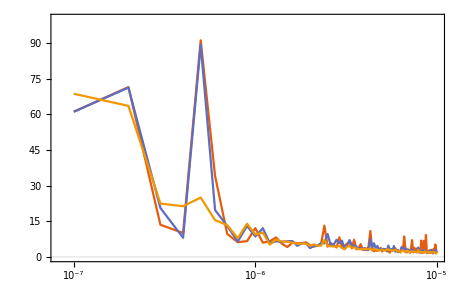

```mathematica
ListLogLinearPlot[{renew0,renew1,renew2},PlotRange->{{0,100}},PlotTheme->"Scientific",Joined->True]
```

## time-avg

```mathematica
Max[Table[((NDS[1 a,1][[1]][t]/((-√(1 a))/(√2 3^0.25 q)))^2+(NDS[1 a,1][[2]][t]/((-√2 √(1 a))/(3 3^0.25 q)))^2+(NDS[1 a,1][[3]][t]/((-√(1 a))/(√2 3^0.75 q)))^2)^0.5,{t,time-π,time,0.1}]]
```

21.0053

```mathematica
renew4=ParallelTable[{(k a m r0^4 Ω^2)/(2 e),1/(√3)Max[Table[((NDS[k a,1][[1]][t]/((-√(k a))/(√2 3^0.25 q)))^2+(NDS[k a,1][[2]][t]/((-√2 √(k a))/(3 3^0.25 q)))^2+(NDS[k a,1][[3]][t]/((-√(k a))/(√2 3^0.75 q)))^2)^0.5,{t,time-π,time,0.1}]]},{k,0.1,10,0.1}]
```

{{1.×10^-7,14.8153},{2.×10^-7,9.77678},{3.×10^-7,8.11231},{4.×10^-7,6.73269},{5.×10^-7,6.32921},{6.×10^-7,5.56388},{7.×10^-7,5.25987},{8.×10^-7,4.95131},{9.×10^-7,4.47769},{1.×10^-6,4.41012},{1.1×10^-6,4.24881},{1.2×10^-6,4.08107},{1.3×10^-6,3.88018},{1.4×10^-6,3.76347},{1.5×10^-6,3.64621},{1.6×10^-6,3.55703},{1.7×10^-6,3.31061},{1.8×10^-6,3.29547},{1.9×10^-6,3.15099},{2.×10^-6,3.11422},{2.1×10^-6,2.95551},{2.2×10^-6,2.99561},{2.3×10^-6,2.88196},{2.4×10^-6,2.77672},{2.5×10^-6,2.66535},{2.6×10^-6,2.82619},{2.7×10^-6,2.65291},{2.8×10^-6,2.67853},{2.9×10^-6,2.68593},{3.×10^-6,2.48008},{3.1×10^-6,2.46944},{3.2×10^-6,2.49576},{3.3×10^-6,2.52822},{3.4×10^-6,2.38704},{3.5×10^-6,2.32713},{3.6×10^-6,2.28081},{3.7×10^-6,2.30381},{3.8×10^-6,2.19466},{3.9×10^-6,2.30359},{4.×10^-6,2.19193},{4.1×10^-6,2.14047},{4.2×10^-6,2.1275},{4.3×10^-6,2.15689},{4.4×10^-6,2.09737},{4.5×10^-6,2.10922},{4.6×10^-6,2.0867},{4.7×10^-6,2.01599},{4.8×10^-6,1.98633},{4.9×10^-6,2.04478},{5.×10^-6,1.90687},{5.1×10^-6,1.92296},{5.2×10^-6,1.99836},{5.3×10^-6,1.95346},{5.4×10^-6,1.86185},{5.5×10^-6,1.89026},{5.6×10^-6,1.88987},{5.7×10^-6,1.80245},{5.8×10^-6,1.87057},{5.9×10^-6,1.8588},{6.×10^-6,1.92062},{6.1×10^-6,1.80204},{6.2×10^-6,1.72715},{6.3×10^-6,1.81373},{6.4×10^-6,1.82644},{6.5×10^-6,1.76187},{6.6×10^-6,1.77991},{6.7×10^-6,1.76912},{6.8×10^-6,1.75084},{6.9×10^-6,1.71721},{7.×10^-6,1.72789},{7.1×10^-6,1.71113},{7.2×10^-6,1.65933},{7.3×10^-6,1.67532},{7.4×10^-6,1.65861},{7.5×10^-6,1.73117},{7.6×10^-6,1.63564},{7.7×10^-6,1.70889},{7.8×10^-6,1.66451},{7.9×10^-6,1.62504},{8.×10^-6,1.61798},{8.1×10^-6,1.65294},{8.2×10^-6,1.51716},{8.3×10^-6,1.60428},{8.4×10^-6,1.53685},{8.5×10^-6,1.60055},{8.6×10^-6,1.55982},{8.7×10^-6,1.5604},{8.8×10^-6,1.59461},{8.9×10^-6,1.57235},{9.×10^-6,1.48511},{9.1×10^-6,1.53147},{9.2×10^-6,1.51857},{9.3×10^-6,1.48955},{9.4×10^-6,1.55645},{9.5×10^-6,1.54719},{9.6×10^-6,1.53096},{9.7×10^-6,1.48402},{9.8×10^-6,1.52628},{9.9×10^-6,1.50892},{0.00001,1.45665}}

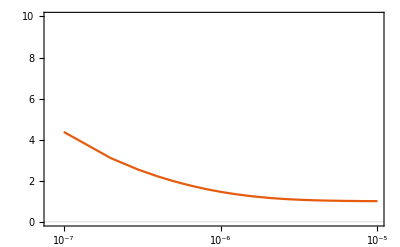

```mathematica
ListLogLinearPlot[{renew},PlotRange->{{0,10}},PlotTheme->"Scientific",Joined->True](*-1*)
```

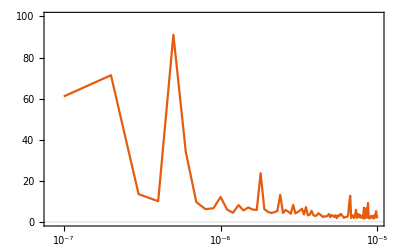

```mathematica
ListLogLinearPlot[{renew2},PlotRange->{{0,100}},PlotTheme->"Scientific",Joined->True](*-4*)
```

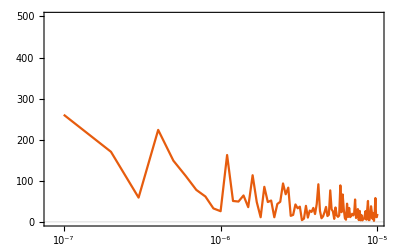

```mathematica
ListLogLinearPlot[{renew3},PlotRange->{{0,500}},PlotTheme->"Scientific",Joined->True](*-6*)
```

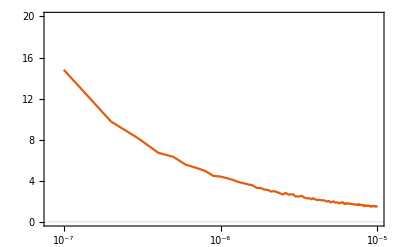

```mathematica
ListLogLinearPlot[{renew4},PlotRange->{{0,20}},PlotTheme->"Scientific",Joined->True](*-3*)
```